```mathematica
ϕ[x_,y_]:=Piecewise[{{1-x-y+x*y, 1≥x≥0&&1≥ y≥0}, {1+x-y-x*y, -1≤x≤0&&1≥y≥0}, {1+x+y+x*y, -1≤x≤0&&-1≤y≤0}, {1-x+y-x*y, 1≥x≥0&&-1≤y≤0}, {0, True}}]
xi = .2; yi = .4;
h = .1;
Plot3D[ϕ[(x-xi)/h,(y-yi)/h],{x,-2,2},{y,-2,2},PlotRange->All,PlotPoints->150]
```

-Graphics3D-

```mathematica
ϕ[(x-xi)/h,(y-yi)/h]
```

Piecewise[{{1-10. (-0.2+x)-10. (-0.4+y)+100. (-0.2+x) (-0.4+y), 1≥10. (-0.2+x)≥0&&1≥10. (-0.4+y)≥0}, {1+10. (-0.2+x)-10. (-0.4+y)-100. (-0.2+x) (-0.4+y), -1≤10. (-0.2+x)≤0&&1≥10. (-0.4+y)≥0}, {1+10. (-0.2+x)+10. (-0.4+y)+100. (-0.2+x) (-0.4+y), -1≤10. (-0.2+x)≤0&&-1≤10. (-0.4+y)≤0}, {1-10. (-0.2+x)+10. (-0.4+y)-100. (-0.2+x) (-0.4+y), 1≥10. (-0.2+x)≥0&&-1≤10. (-0.4+y)≤0}, {0, True}}]

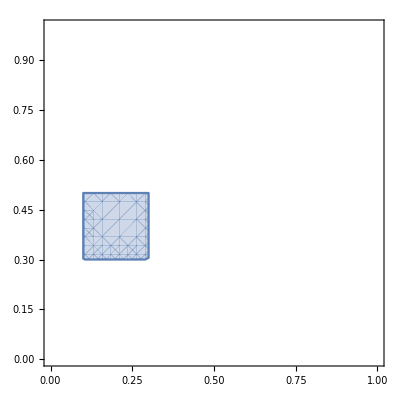

-Graphics3D-

```mathematica
RegionPlot[1≥10. (-0.2+x)≥0&&1≥10. (-0.4+y)≥0||-1≤10. (-0.2+x)≤0&&1≥10. (-0.4+y)≥0||-1≤10. (-0.2+x)≤0&&-1≤10. (-0.4+y)≤0||1≥10. (-0.2+x)≥0&&-1≤10. (-0.4+y)≤0,{x,0,1},{y,0,1}]
```

```mathematica
a=-1;
b=1;
xi=0;
yi = 0;
h = 0.5;
Plot3D[ϕ[(x-xi)*h,(y-yi)*h],{x,a,b},{y,a,b},PlotRange->All]
```

-Graphics3D-

```mathematica
ϕ[0,0]
```

1

```mathematica
ϕ[(x-xi)/h,(y-yi)/h]
```

Piecewise[{{1-2. (-2+x)-2. (-1+y)+4. (-2+x) (-1+y), 1≥2. (-2+x)≥0&&1≥2. (-1+y)≥0}, {1+2. (-2+x)-2. (-1+y)-4. (-2+x) (-1+y), -1≤2. (-2+x)≤0&&1≥2. (-1+y)≥0}, {1+2. (-2+x)+2. (-1+y)+4. (-2+x) (-1+y), -1≤2. (-2+x)≤0&&-1≤2. (-1+y)≤0}, {1-2. (-2+x)+2. (-1+y)-4. (-2+x) (-1+y), 1≥2. (-2+x)≥0&&-1≤2. (-1+y)≤0}, {0, True}}]

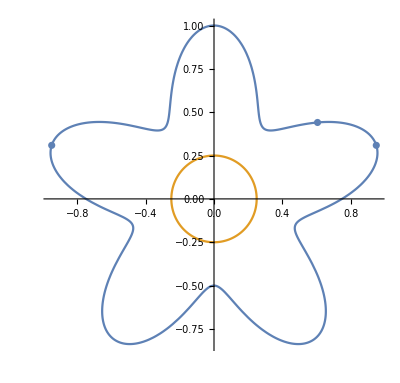

```mathematica
fo[r_,θ_]:=r - 0.75-0.25*Sin[5θ];
Show[PolarPlot[{0.75+0.25*Sin[5θ],.25},{θ,0,2 π}],ListPlot[{{Cos[π/10],Sin[π/10]},{0.75Cos[2π/10],0.75Sin[2π/10]},{Cos[9π/10],Sin[9π/10]}}]]
```

```mathematica
5*θ == π/2
```

```mathematica
??PolarPlot
```

PolarPlot[r,{θ,θ_min,θ_max}] generates a polar plot of a curve with radius r as a function of angle θ.
PolarPlot[{f_1,f_2,…},{θ,θ_min,θ_max}] makes a polar plot of curves with radius functions f_1, f_2, ….

Attributes[PolarPlot]={Protected,ReadProtected}

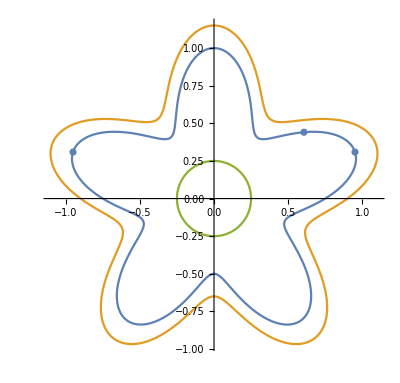

```mathematica
fo[θ_]:= 0.75+0.25*Sin[5θ];
fo1[θ_]:= .9+0.25*Sin[5θ];
Show[PolarPlot[{fo[θ],fo1[θ],.25},{θ,0,2 π}],ListPlot[{{Cos[π/10],Sin[π/10]},{0.75Cos[2π/10],0.75Sin[2π/10]},{Cos[9π/10],Sin[9π/10]}}]]
```